Simple Model  of a Neuron

Exercise 1: First numerical exploration

```mathematica
ClearAll["Global'*"]
```

```mathematica
f[v_,w_]=((a - v)(v -1) v -w)/e;
g[v_,w_]=b v - r w + c;
```

```mathematica
s1 = {a -> -1,b -> 0.12,c -> 0, e -> 1, r -> 0.12};
s2 = {a -> -1,b -> 0.06,c -> 0, e -> 1, r -> 0.12};
s3 = {a -> -1,b -> 0.12,c -> -0.1, e -> 1, r -> 0.12};
s4 = {a -> -1,b -> 0.12,c -> 0, e -> 0.1, r -> 0.12};
```

(-1-v) (-1+v) v-w

0.12 v-0.12 w

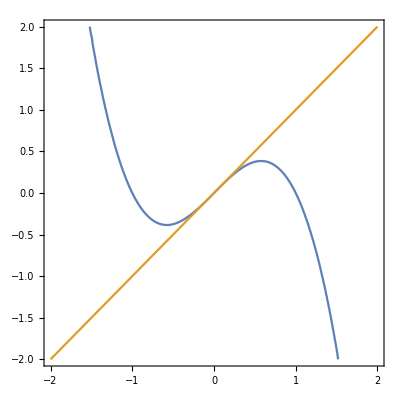

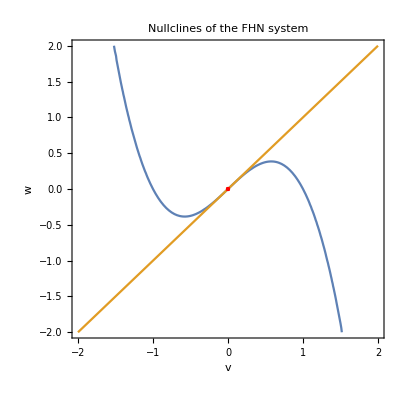

```mathematica
ff [v_,w_]= f[v,w]/.s1
gg[v_,w_] = g[v,w] /.s1
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}]
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.ptRules}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system ],LabelStyle->{GrayLevel[0]},Axes->True]
```

(-1-v) (-1+v) v-w

0.06 v-0.12 w

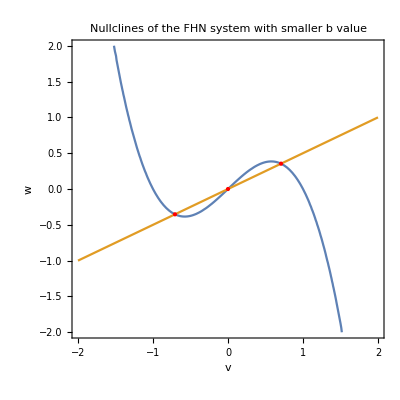

```mathematica
ff [v_,w_]= f[v,w]/.s2
gg[v_,w_] = g[v,w] /.s2
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.ptRules}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system with smaller b value],LabelStyle->{GrayLevel[0]},Axes->True]
```

```mathematica
(*Cases[ptRules,n_List /; ( Element[({v,w}/. n1)[[1]],Reals]&& .Element[({v,w}/. n1)[[2]],Reals])]*)
```

(-1-v) (-1+v) v-w

-0.1+0.12 v-0.12 w

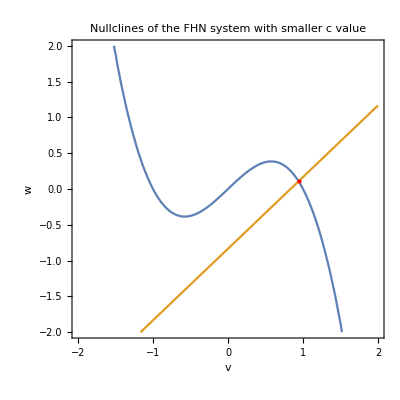

```mathematica
ff [v_,w_]= f[v,w]/.s3
gg[v_,w_] = g[v,w] /.s3
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system with smaller c value],LabelStyle->{GrayLevel[0]},Axes->True]
```

```mathematica
(* /; means condition, n_List : n is the name, while _List shows the type *)
(* The reason why we need this cases is that there are solutions that are complex, and since I directly substitute the points and plot it, the complex points cannot be plotted, in this way, it only takes the Real points *)
```

10. ((-1-v) (-1+v) v-w)

0.12 v-0.12 w

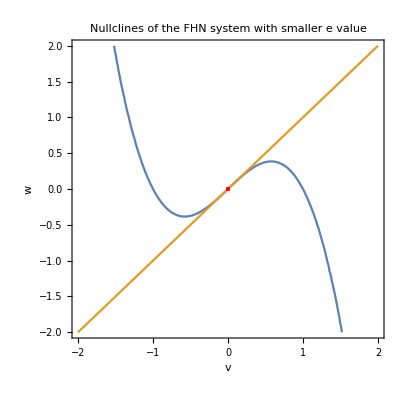

```mathematica
ff [v_,w_]= f[v,w]/.s4
gg[v_,w_] = g[v,w] /.s4
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.ptRules}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system with smaller e value],LabelStyle->{GrayLevel[0]},Axes->True]
```

From the plots above, the alteration of b value changes the slope of the linear nullcline. The alteration of the c value changes the intersect of the linear nullcline and the horizontal and vertical axis. The alteration of the e value, we cannot see the difference from the plot, since e is changing the speed of the excitable behavior, we will see the difference from v-t plot.

Exercise 2: Excitability

```mathematica
s5 = {a -> -1,b -> 0.12,c -> 0.03, e -> 1, r -> 0.12};
```

```mathematica
ff [v_,w_]= f[v,w]/.s5
gg[v_,w_] = g[v,w] /.s5
```

(-1-v) (-1+v) v-w

0.03+0.12 v-0.12 w

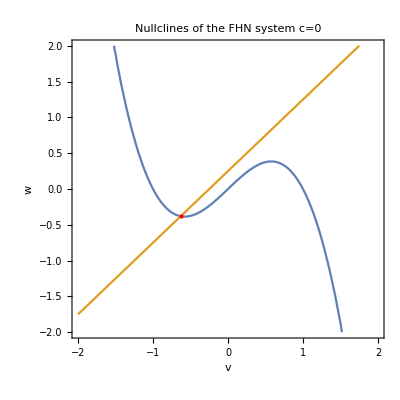

```mathematica
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
pl1 =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system c = 0],LabelStyle->{GrayLevel[0]},Axes->True]
```

```mathematica
sol=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.s5,w'[t]==b v [t]- r w[t] + c/.s5,v[0]==w[0]==0.5},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

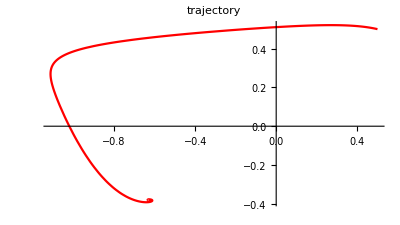

```mathematica
pl2 =ParametricPlot[Evaluate[{v[t],w[t]}/.sol],{t,0,100},PlotRange->All,PlotStyle->Red,PlotLabel->"trajectory"]
```

```mathematica
v[t]/.sol
```

{InterpolatingFunction[…][t]}

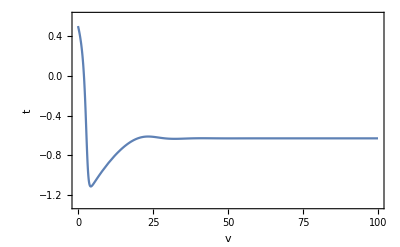

```mathematica
Plot[v[t] /. sol,{t,0,100},Frame -> True,FrameLabel -> {v,t},LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> {-1.3, 0.6}]
```

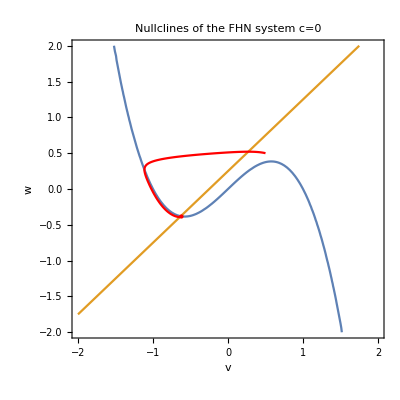

```mathematica
Show[pl1,pl2]
```

```mathematica
sol001=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.s5,w'[t]==b v [t]- r w[t] + c/.s5,v[0]== Flatten[v[100]/.sol][[1]] + 0.01,w[0]==Flatten[w[100]/.sol][[1]]},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
pl5 = Plot[v[t] /. sol001,{t,0,100}, Frame -> True,FrameLabel -> {v,t},LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> {-1.3, 6}];
pl7 = Plot[w[t] /. sol001,{t,0,100}, Frame -> True,FrameLabel -> {w,t},LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> {-0.45, 0.6}];
```

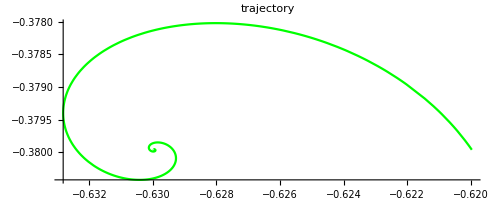

```mathematica
pl3 =ParametricPlot[Evaluate[{v[t],w[t]}/.sol001],{t,0,100},PlotRange->All,PlotStyle->Green,PlotLabel->"trajectory"]
```

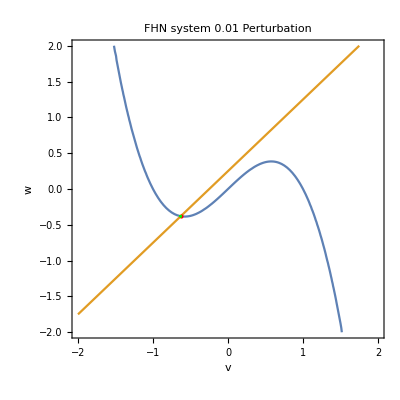

```mathematica
ppll1 = Show[pl1,pl3,PlotLabel->HoldForm[FHN system 0.01 Perturbation]]
```

```mathematica
sol03=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.s5,w'[t]==b v [t]- r w[t] + c/.s5,v[0]== Flatten[v[100]/.sol][[1]] + 0.3,w[0]==Flatten[w[100]/.sol][[1]]},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
pl6 = Plot[v[t] /. sol03,{t,0,100}, Frame -> True,FrameLabel -> {v,t},LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> {-1.3, 1}];
pl8 = Plot[w[t] /. sol03,{t,0,100}, Frame -> True,FrameLabel -> {w,t},LabelStyle->{GrayLevel[0]},Axes->True, PlotRange-> {-0.45, 0.6}];
```

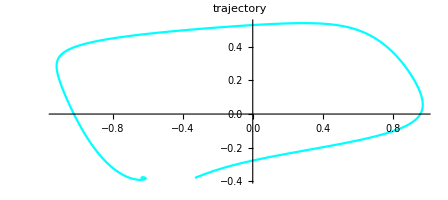

```mathematica
pl4 =ParametricPlot[Evaluate[{v[t],w[t]}/.sol03],{t,0,100},PlotRange->All,PlotStyle->Cyan,PlotLabel->"trajectory"]
```

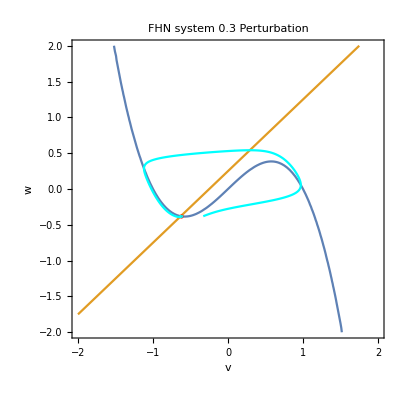

```mathematica
ppll2 = Show[pl1,pl4,PlotLabel->HoldForm[FHN system 0.3 Perturbation]]
```

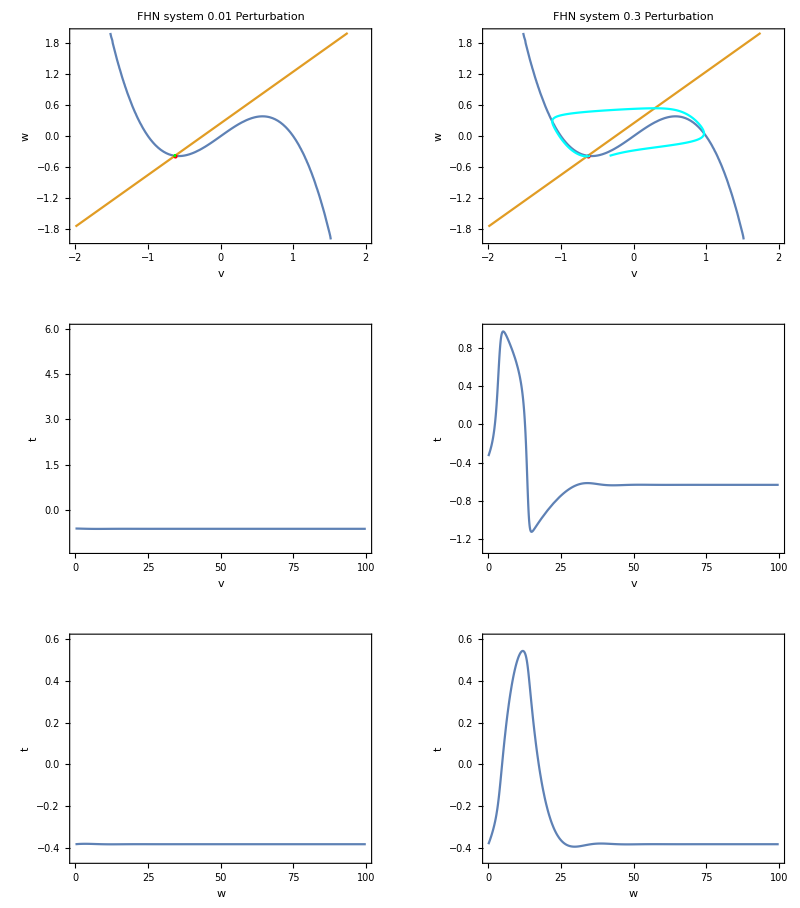

```mathematica
GraphicsGrid[{{ppll1,ppll2},{pl5,pl6},{pl7,pl8}}]
```

The left column is from the 0.01 perturbation, and the right column is from the 0.3 perturbation. For the v-t plot, we can barely see any changes for the 0.01 case, but a huge spike in the 0.3 case. For the w-t plot, we can barely see any changes for the 0.01 case, but a significant increase in the 0.3 case.  Linking with the nullclines, we can see that a bigger perturbation that passes the linear nullcline has a large trajectory when aiming to go back to the stable point, and thus we see the spike in the v-t plot.

FHN system is mathematically simple and produces dynamics of biophysical neuron. This system simulate that if there is a large change, then there is the spike, while in case of small changes, there is barely a difference.

Exercise 3: Linear Stability Analysis

```mathematica
se1 = {a -> -1,b -> 0.12,c -> -0.2, e -> 1, r -> 0.12};
```

```mathematica
ff [v_,w_]= f[v,w]/.se1
gg[v_,w_] = g[v,w] /.se1
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system c = -0.2],LabelStyle->{GrayLevel[0]},Axes->True];
```

(-1-v) (-1+v) v-w

-0.2+0.12 v-0.12 w

```mathematica
solse1=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se1,w'[t]==b v [t]- r w[t] + c/.se1,v[0]== 1, w[0]==1},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
plse1 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse1],{t,0,100},PlotRange->All,PlotStyle->Red];
```

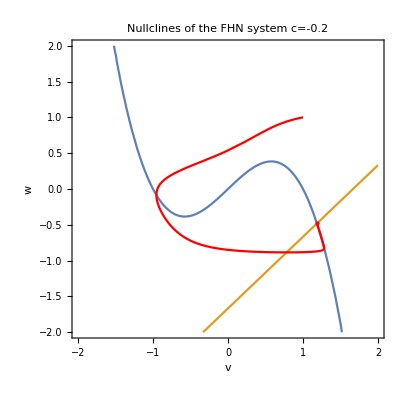

```mathematica
Show[plse, plse1]
```

```mathematica
p = {f[v,w]/.se1,g[v,w] /. se1};
q = {v,w};
J1[v_,w_] = Grad[p,q]  ;
```

```mathematica
J1[v,w] /. {v -> 1, w -> 1}
```

{{-2,-1},{0.12,-0.12}}

```mathematica
Eigenvalues[J1[v,w] /. {v -> 1, w -> 1}]
```

{-1.93384,-0.186158}

The eigen value {-1.93384,-0.186158} of the Jacobian matrix are negative, this means that it converges to the fixed point (the red point in the plot).

```mathematica
Eigenvalues[J1[v,w] /. Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]]
```

{-3.17792,-0.159242}

{-3.17792,-0.159242} is the eigen values at the fixed points, both are negative.

```mathematica
se2 = {a -> -1,b -> 0.12,c -> -0.01, e -> 1, r -> 0.12};
```

```mathematica
ff [v_,w_]= f[v,w]/.se2
gg[v_,w_] = g[v,w] /.se2
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system c = -0.01],LabelStyle->{GrayLevel[0]},Axes->True];
```

(-1-v) (-1+v) v-w

-0.01+0.12 v-0.12 w

```mathematica
solse2=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se2,w'[t]==b v [t]- r w[t] + c/.se2,v[0]==w[0]==1},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
plse2 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse2],{t,0,100},PlotRange->All,PlotStyle->Cyan];
```

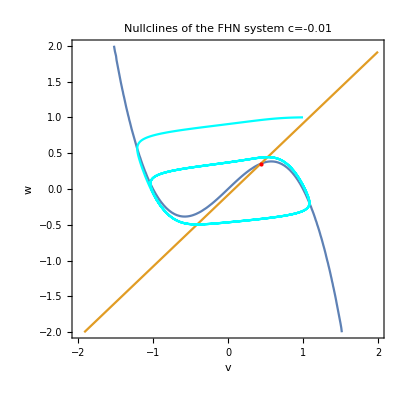

```mathematica
Show[plse, plse2]
```

```mathematica
p = {f[v,w] /. se2,g[v,w] /. se2};
q = {v,w};
J2[v_,w_] = Grad[p,q]  ;
```

```mathematica
Eigenvalues[J2[v,w] /. {v -> 1, w -> 1}]
```

{-1.18584,-0.358846}

```mathematica
Eigenvalues[J2[v,w] /. Flatten[Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]]]
```

{-1.44455,-0.071011}

At the initial point, the eigen values {-1.18584,-0.358846} are both negative, and at the fixed points, the eigen values {-1.44455,-0.071011} are both negative as well. As we can see from the above plot, the point is converging to the fixed point.

```mathematica
Clear[a,b,c,e,r]
```

```mathematica
se3= {a -> -1,b -> 0.12,c -> 0.15, e -> 1, r -> 0.12}
```

{a→-1,b→0.12,c→0.15,e→1,r→0.12}

```mathematica
ff [v_,w_]= f[v,w]/.se3
gg[v_,w_] = g[v,w] /.se3
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system c = 0.15],LabelStyle->{GrayLevel[0]},Axes->True];
```

(-1-v) (-1+v) v-w

0.15+0.12 v-0.12 w

```mathematica
solse3=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se3,w'[t]==b v [t]- r w[t] + c/.se3,v[0]==w[0]==1},{v,w},{t,100}]
```

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
plse3 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse3],{t,0,100},PlotRange->All,PlotStyle->Green];
```

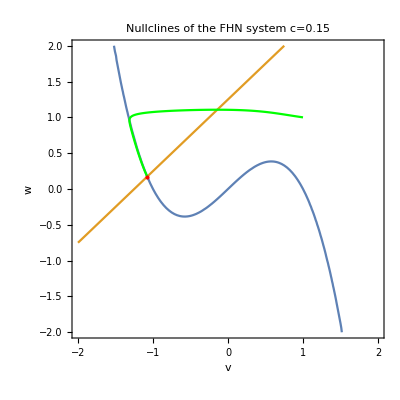

```mathematica
Show[plse, plse3]
```

```mathematica
p = {f[v,w] /. se3,g[v,w] /. se3};
q = {v,w};
J3[v_,w_] = Grad[p,q]
```

{{(-1-v) (-1+v)+(-1-v) v-(-1+v) v,-1},{0.12,-0.12}}

```mathematica
mmm = J3[v,w]/.ptRules
```

{{{2.7406+3.0148 ⅈ,-1},{0.12,-0.12}},{{2.7406-3.0148 ⅈ,-1},{0.12,-0.12}},{{-2.48119,-1},{0.12,-0.12}}}

```mathematica
Eigenvalues[mmm[[1]]]
```

{2.72088+3.03587 ⅈ,-0.10028-0.0210738 ⅈ}

```mathematica
Eigenvalues[mmm[[2]]]
```

{2.72088-3.03587 ⅈ,-0.10028+0.0210738 ⅈ}

```mathematica
Eigenvalues[mmm[[3]]]
```

{-2.42923,-0.171965}

```mathematica
Eigenvalues[J3[v,w] /. {v -> 1, w -> 1}]
```

{-1.93384,-0.186158}

The eigen values {-1.93384,-0.186158} at  the initial point are both negative.   The eigen values {-2.42923,-0.171965} at the fixed point are both negative. The eigen values at the two complex fix points are one positive and one negative. As we can see from the above plot, the point is converging to the real fixed point. For different values of c, the eigen values at the real fixed point  are negative.

```mathematica
Clear[v,w,a,b,c,e,r]
```

```mathematica
se4= {a -> -1,b -> 0.1,c -> 0, e -> 1, r -> 0.12};
```

(-1-v) (-1+v) v-w

0.1 v-0.12 w

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

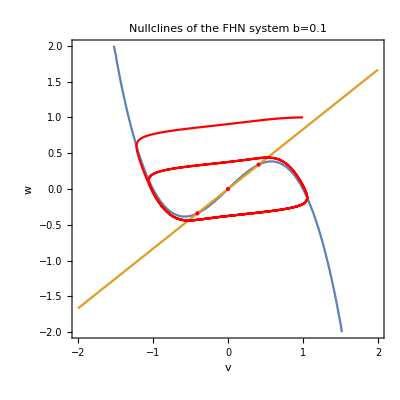

```mathematica
ff [v_,w_]= f[v,w]/.se4
gg[v_,w_] = g[v,w] /.se4
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system b = 0.1],LabelStyle->{GrayLevel[0]},Axes->True];
solse4=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se4,w'[t]==b v [t]- r w[t] + c/.se4,v[0]==w[0]==1},{v,w},{t,100}]
plse4 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse4],{t,0,100},PlotRange->All,PlotStyle->Red];
Show[plse, plse4]
```

```mathematica
a = {f[v,w] /. se4,g[v,w] /. se4};
b = {v,w};
J4[v_,w_] = Grad[a,b]  ;
Eigenvalues[J4[v,w] /. {v -> 1, w -> 1}]
```

{-1.94521,-0.174788}

```mathematica
ptRules
```

{{v→0.408248,w→0.340207},{v→-0.408248,w→-0.340207},{v→0.,w→0.}}

```mathematica
m4 = J4[v,w] /.ptRules
```

{{{0.5,-1},{0.1,-0.12}},{{0.5,-1},{0.1,-0.12}},{{1.,-1},{0.1,-0.12}}}

```mathematica
Eigenvalues[m4[[1]]]
```

{0.19+0.06245 ⅈ,0.19-0.06245 ⅈ}

```mathematica
Eigenvalues[m4[[2]]]
```

{0.19+0.06245 ⅈ,0.19-0.06245 ⅈ}

```mathematica
Eigenvalues[m4[[3]]]
```

{0.902169,-0.0221688}

Here, b = 0.1, at the initial point (1,1) the eigen values are both negative, and thus, it is converging to the fixed points. At fixed points, the middle one (0,0) has one positive and one negative eigen values, while at the other two real fixed points the real part of the eigen values are all positive, which means diverging from the fixed points. As we can see in the plot, the trajectory does not end at either fixed points (red dots).

```mathematica
Clear[v,w,a,b,c,e,r]
```

```mathematica
se5= {a -> -1,b -> 0.35,c -> 0, e -> 1, r -> 0.12};
```

(-1-v) (-1+v) v-w

0.35 v-0.12 w

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

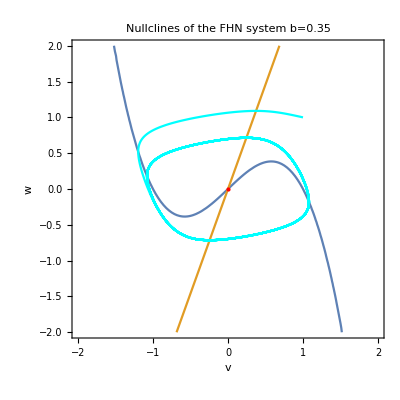

```mathematica
ff [v_,w_]= f[v,w]/.se5
gg[v_,w_] = g[v,w] /.se5
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system b = 0.35],LabelStyle->{GrayLevel[0]},Axes->True];
solse5=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se5,w'[t]==b v [t]- r w[t] + c/.se5,v[0]==w[0]==1},{v,w},{t,100}]
plse5 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse5],{t,0,100},PlotRange->All,PlotStyle->Cyan];
Show[plse, plse5]
```

```mathematica
a = {f[v,w] /. se5,g[v,w] /. se5};
b = {v,w};
J5[v_,w_] = Grad[a,b]  ;
Eigenvalues[J5[v,w] /. {v -> 1, w -> 1}]
```

{-1.79048,-0.329521}

```mathematica
m5  = J5[v,w] /.ptRules
```

{{{6.75+0. ⅈ,-1},{0.35,-0.12}},{{6.75+0. ⅈ,-1},{0.35,-0.12}},{{1.,-1},{0.35,-0.12}}}

```mathematica
Eigenvalues[m5[[1]]]
```

{6.69867,-0.0686703}

```mathematica
Eigenvalues[m5[[2]]]
```

{6.69867,-0.0686703}

```mathematica
Eigenvalues[m5[[3]]]
```

{0.44+0.190788 ⅈ,0.44-0.190788 ⅈ}

Here, b = 0.35, and there is only one real fixed points, where both eigen values are positive, meaning divergence. For the two complex fixed points, one eigen value is positive, while the other is negative. As we can see in the plot, the trajectory does not end at fixed point.

```mathematica
Clear[v,w,a,b,c,e,r]
```

```mathematica
se6= {a -> -1,b -> 0.58,c -> 0, e -> 1, r -> 0.12};
```

(-1-v) (-1+v) v-w

0.58 v-0.12 w

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

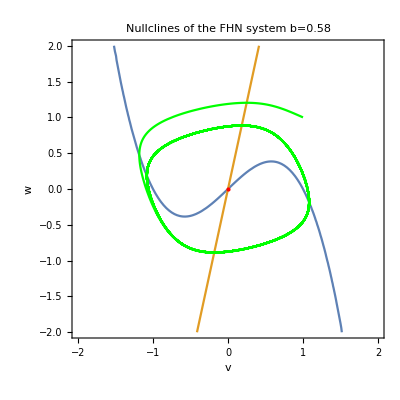

```mathematica
ff [v_,w_]= f[v,w]/.se6
gg[v_,w_] = g[v,w] /.se6
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plse =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system b = 0.58],LabelStyle->{GrayLevel[0]},Axes->True];
solse6=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.se6,w'[t]==b v [t]- r w[t] + c/.se6,v[0]==w[0]==1},{v,w},{t,100}]
plse6 =ParametricPlot[Evaluate[{v[t],w[t]}/.solse6],{t,0,100},PlotRange->All,PlotStyle->Green];
Show[plse, plse6]
```

```mathematica
a = {f[v,w] /. se6,g[v,w] /. se6};
b = {v,w};
J6[v_,w_] = Grad[a,b]  ;
Eigenvalues[J6[v,w] /. {v -> 1, w -> 1}]
```

{-1.611,-0.509001}

```mathematica
m6 = J6[v,w] /. ptRules
```

{{{12.5+0. ⅈ,-1},{0.58,-0.12}},{{12.5+0. ⅈ,-1},{0.58,-0.12}},{{1.,-1},{0.58,-0.12}}}

```mathematica
Eigenvalues[m6[[1]]]
```

{12.4539,-0.0738726}

```mathematica
Eigenvalues[m6[[2]]]
```

{12.4539,-0.0738726}

```mathematica
Eigenvalues[m6[[3]]]
```

{0.44+0.51614 ⅈ,0.44-0.51614 ⅈ}

Here, b = 0.58, and there is only one real fixed points, where both eigen values are positive, meaning divergence. For the two complex fixed points, one eigen value is positive, while the other is negative. As we can see in the plot, the trajectory does not end at fixed point.

In order to reach bistable behavior, two Jacobian matrices needs to be positive definite, i.e. all eigen values are positive. Therefore, as far as the b values satisfying such statements, it displays bistable behavior, which is [0.1, 0.12)

```mathematica
Clear[v,w,a,b,c,e,r]
```

```mathematica
ss= {a -> -1,b -> 0.12,c -> 0, e -> 1, r -> 0.12};
```

(-1-v) (-1+v) v-w

0.12 v-0.12 w

{{v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

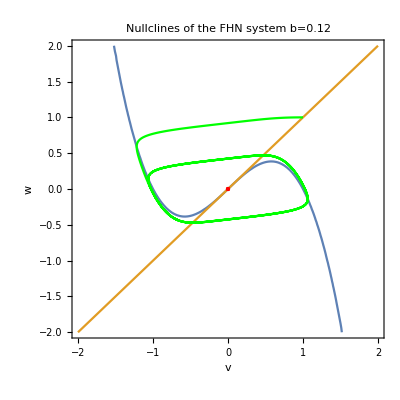

```mathematica
ff [v_,w_]= f[v,w]/.ss
gg[v_,w_] = g[v,w] /.ss
cp=ContourPlot[{ff[v,w]==0,gg[v,w]==0},{v,-2,2},{w,-2,2}];
ptRules=NSolve[{ff[v,w]==0,gg[v,w]==0},{v,w}];
plss =Show[cp,Graphics[{Red,PointSize[Large],Point[{v,w}]/.Cases[ptRules,n_List /; ( Element[({v,w}/. n)[[1]],Reals]&& Element[({v,w}/. n)[[2]],Reals])]}],FrameLabel->{{HoldForm[w],None},{HoldForm[v],None}},PlotLabel->HoldForm[Nullclines of the FHN system b = 0.12],LabelStyle->{GrayLevel[0]},Axes->True];
solss=NDSolve[{v'[t]==((a - v[t])(v[t] -1) v[t] -w[t])/e/.ss,w'[t]==b v [t]- r w[t] + c/.ss,v[0]==w[0]==1},{v,w},{t,100}]
plsss =ParametricPlot[Evaluate[{v[t],w[t]}/.solss],{t,0,100},PlotRange->All,PlotStyle->Green];
Show[plss, plsss]
```

```mathematica
p = {f[v,w] /. ss,g[v,w] /. ss};
q = {v,w};
J[v_,w_] = Grad[p,q]  ;
kk = J[v,w] /. ptRules
Eigenvalues[kk[[1]]]
Eigenvalues[kk[[2]]]
Eigenvalues[kk[[3]]]
```

{{{1.,-1},{0.12,-0.12}},{{1.,-1},{0.12,-0.12}},{{1.,-1},{0.12,-0.12}}}

{0.88,0.}

{0.88,0.}

{0.88,0.}

Here shows the critical point such that the bistable behavior vanishes.